```mathematica
data={{0,0.45/0.45 210},{0.001,0.454577/0.45 210},{0.002,0.459081/0.45 210},{0.005,0.472155/0.45 210},{0.01 ,0.492564/0.45 210},{0.02,0.528701/0.45 210},{0.03,0.559411/0.45 210},{0.04,0.585539/0.45 210},{0.05,0.607799/0.45 210},{0.06,0.626794/0.45 210},{0.07,0.643032/0.45 210},{0.08,0.656942/0.45 210},{0.09,0.668887/0.45 210},{0.10 ,0.679172/0.45 210},{0.12 ,0.695760/0.45 210},{0.14 ,0.708326/0.45 210},{0.16 ,0.718025/0.45 210},{0.20 ,0.731879/0.45 210},{0.25 ,0.743463/0.45 210},{0.3 ,0.752122/0.45 210},{0.5 ,0.779564/0.45 210},{1.0 ,0.84424/0.45 210},{11.0 ,2.13664/0.45 210}};
```

```mathematica
PLFUN[epbar_,data_]:=Block[{sigy,H},
sigy=Interpolation[data];
H=sigy';
{sigy[epbar],H[epbar]}
]
```

```mathematica
PLFUN[0.1,data]
```

{316.947,445.114}

```mathematica
ApplyStrainComputeStress[epst_,epsp_,young_,nu_,epbarn_,flag_]:=Block[{d,resnor,counter,ddgamma,epbar,sigy,q,H=0,G,K,trialstrain,updatedstrain,trialstress,S,P,j2,phi,gamma,updatedstress,hardeningvariable,Dep,qtr,Str,trSS,tol,sigxx,sigyy,sigxy,Nvec,epsxx,epsyy,epsxy,sigzz,lambda,mu,J2,Mult},

Sigma[eps_]:=lambda Tr[eps]IdentityMatrix[3]+2 mu eps;
G=(young)/(2*(1+nu));
K=(young)/(3*(1-2nu));
lambda=young nu/((1+nu)(1-2nu));
mu=young/(2(1+nu));

trialstrain=(epst-epsp);
{epsxx,epsyy,epsxy}={trialstrain[[1,1]],trialstrain[[2,2]],trialstrain[[1,2]]};
If[flag==1,
(*Plane Stress*)
(*nao funciona*)
trialstress={{-((epsxx+epsyy nu) young)/(-1+nu^2),(epsxy young)/(2+2 nu),0},{(epsxy young)/(2+2 nu),-((epsyy+epsxx nu) young)/(-1+nu^2),0},{0,0,0}};
];
If[flag==2,
(*Plane Strain*)
trialstress={{((epsxx (-1+nu)-epsyy nu) young)/(-1+nu+2 nu^2),(epsxy young)/(1+nu),0},{(epsxy young)/(1+nu),((epsyy (-1+nu)-epsxx nu) young)/(-1+nu+2 nu^2),0},{0,0,-((epsxx+epsyy) nu young)/(-1+nu+2 nu^2)}};
];
If[flag==3,
(*3D*)
trialstress=Sigma[trialstrain];
];

hardeningvariable=epbarn;

P=1/3 Tr[trialstress];
S=trialstress-1/3 Tr[trialstress]IdentityMatrix[3];
J2=1/2 Tr[S.S];
q=Sqrt[3 J2];

Nvec=S/Norm[S];
{sigy,H}= PLFUN[epbarn,data];
phi=q-sigy;
gamma=0;
If[phi≥ 0,
counter=1;
epbar=epbarn;
(*Print[" epbar  = ",epbar];*)
resnor=1;
tol=10^-5;
While[resnor≥ tol && counter<30,
{sigy,H}=PLFUN[epbar,data];
(*{sigy,H}={210,0};*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigy;
resnor=Abs[phi/sigy];
counter++;

];
Mult=(1-((gamma 3 G )/q));
(*Print["milt = ",Mult];*)
S=Mult S;
updatedstrain=(1/(2G) S+ 1/3 Tr[trialstrain]IdentityMatrix[3]);
updatedstress=( P IdentityMatrix[3]+  S);
hardeningvariable+=gamma;
,
updatedstrain=trialstrain;
updatedstress=( P IdentityMatrix[3]+  S);

];

{updatedstrain,updatedstress,hardeningvariable,Dep,Nvec}

]
```

```mathematica
young=210000;
nu=0.3;
sigy=210;
steps=1000;
loadsize=50
```

50

```mathematica
(*deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,1];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot1=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"}]*)
```

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,2];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot1=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},PlotStyle->{Red,Dashed}];

solpsy=Table[epsvec[[i,1,1]]-epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
plot2=ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx-ϵy","σx-σy"},PlotStyle->{Red,Dashed}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,3];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot3=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"}];

solpsy=Table[epsvec[[i,1,1]]-epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
plot4=ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx-ϵy","σx-σy"}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

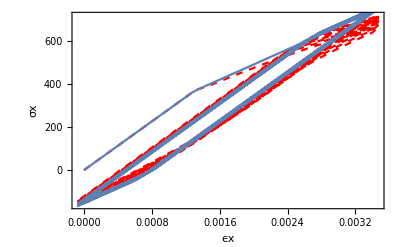

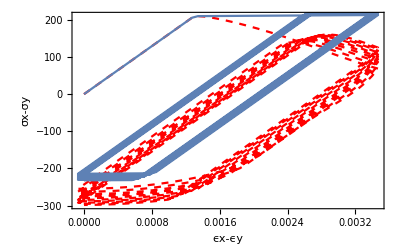

```mathematica
Show[plot1,plot3]
Show[plot2,plot4]
```

```mathematica
young=210000;
nu=0.;
sigy=210;
steps=1000;
loadsize=50
```

50

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,2];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot1=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},PlotStyle->{Red,Dashed}];

solpsy=Table[epsvec[[i,1,1]]-epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
plot2=ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx-ϵy","σx-σy"},PlotStyle->{Red,Dashed}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,3];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot3=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"}];

solpsy=Table[epsvec[[i,1,1]]-epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
plot4=ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx-ϵy","σx-σy"}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

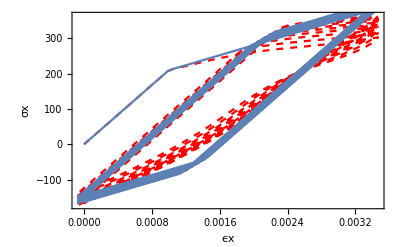

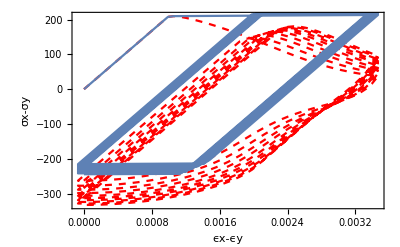

```mathematica
Show[plot1,plot3]
Show[plot2,plot4]
```

```mathematica
young=210000;
nu=0.499;
sigy=210;
steps=1000;
loadsize=50
```

50

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,2];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot1=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"},PlotStyle->{Red,Dashed}];

solpsy=Table[epsvec[[i,1,1]]-epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
plot2=ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx-ϵy","σx-σy"},PlotStyle->{Red,Dashed}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
deps={{0.0000353745,0,0},{0,0,0},{0,0,0}}2;
(*epst={{0.0000353745,0,0},{0,0,0},{0,0,0}}2 15;*)
epst={{0.,0,0},{0,0,0},{0,0,0}};
epsp={{0,0,0},{0,0,0},{0,0,0}}/2;
hard=0.;
epsvec={};
sigvec={};
hardvec={};
For[i=1,i<steps,i++,

hard0=hard;
{eps,stress,hard,Dep,Nvec}=ApplyStrainComputeStress[epst,epsp,young,nu,hard0,3];
(*hard+=hard0;*)
diff=Simplify[De-Dep];
epsp=epst-eps;
AppendTo[epsvec,epst];
AppendTo[sigvec,stress];
AppendTo[hardvec,hard];
If[ Mod[i,loadsize]==0,
deps*=-1;
];
epst+=deps;
];
solpsx=Table[epsvec[[i,1,1]],{i,1,Length[epsvec]}];
solsigx=Table[sigvec[[i,1,1]],{i,1,Length[sigvec]}];
plot3=ListLinePlot[Table[Tooltip[{solpsx[[i]],solsigx[[i]]}],{i,1,Length[solpsx]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx","σx"}];

solpsy=Table[epsvec[[i,1,1]]-epsvec[[i,2,2]],{i,1,Length[epsvec]}];
solsigy=Table[sigvec[[i,1,1]]-sigvec[[i,2,2]],{i,1,Length[sigvec]}];
plot4=ListLinePlot[Table[Tooltip[{solpsy[[i]],solsigy[[i]]}],{i,1,Length[solpsy]}],AxesOrigin->{0,0},Frame->True,FrameLabel->{"ϵx-ϵy","σx-σy"}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

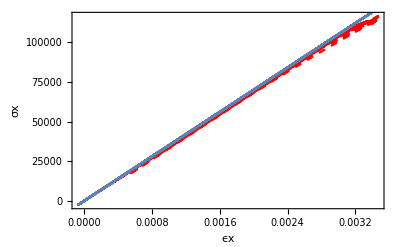

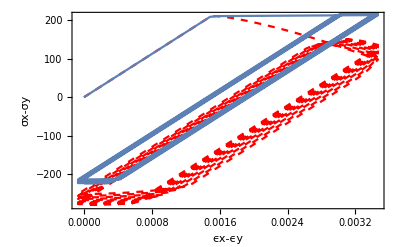

```mathematica
Show[plot1,plot3]
Show[plot2,plot4]
```